# Homework 3 machine learning

## Data preprocessing

```mathematica
"Different preprocessing can lead to various results, so our group tried three different preprocessing methods for our training data:
1. Remove stopwords & high-frequency meaningless words,because those words are selected by ourselves, we need to check whether those words affect training result or not.
2. Remove stopwords, this is used to compare with the first method to make sure the word we removed doesn't affect result
3. Don't remove anything. Because removing words can cause information losing. We need to show that the lost information doesn't affect result"
```

### Remove stopwords + remove some meaningless words

```mathematica
raw=OpenRead["~/Documents/reviews.csv"];
reviews=Map[StringSplit[#,"|"]&,ReadList[raw,String]];
For[i=2,i≤Length[reviews],i++,reviews[[i,2]]=ToLowerCase[reviews[[i,2]]]];
(*Delete punctuation*)
For[i=2,i≤Length[reviews],i++,reviews[[i,2]]=StringReplace[reviews[[i,2]],PunctuationCharacter->" "]]
(*Delete stopwords*)
For[i=2,i≤Length[reviews],i++,reviews[[i,2]]=DeleteStopwords[reviews[[i,2]]]]
(*Remove some useless words*)
For[i=2,i≤Length[reviews],i++,reviews[[i,2]]=StringReplace[reviews[[i,2]]," t "|" s "|" m "|" ll "|" re "|" ve "| " d "|" book "|" just "|" read "|" time "|" movie "|" buy "|" product "|" cd "|" use "|" work "|" bought "|" m "|" album "|" new "|" way "|" story "|" money "|" think "|" music "|" make "|" got "|" know "|" people "|" books "|" years "|" used "|" dvd "|" go "|" game "|" another "|" found "|" reading "|" say "|" life "|" while "|" songs "|" thing "|" thought "|" price "|" film "|" works "|" amazon "|" sound "|" year "|" looking "|" going "|" characters "|" day "|" look "|" author "|" set "|" series "|" times "|" makes "|" written "|" end "|" watch "|" purchased "|" song "|" feel "|" reviews "|" come "|" using "|" play "|" away "|" things "|" version "|" bit "|" stars "|" came "|" review "|" item "|" months "|" said "|" video "|" getting "|" purchase "|" writing "|" plot "|" information "|" several "|" days "|" star "|" man "|" band "|" let "|" movies "|" live "|" buying "|" received "|" trying "|" heard "|" box "|" ordered "|" ago "|" character "|" job "|" home "|" listen "|" took "|" cover "|" looks "|" kids "|" family "|" case "|" went "|" point "|" order "|" stuff "|" minutes "|" place "|" water "|" collection "|" history "|" son "|" pages "|" style "|" children "|" between "|" left "|" line "|" gets "|" comes "|" unit "|" working "|" making "|" start "|" saw "|" size "|" picture "|" myself "|" voice "|" side "|" tell "|" rock "|" tv "|" etc "|" hear "|" couple "|" christmas "|" stories "|" black "|" gift "|" person "|" page "|" daughter "|" camera "|" player "|" watching "|" battery "|" phone "|" reader "|" service "|" hours "|" child "|" company "|" night "|" words "|" school "|" track "|" felt "|" thinking "|" today "|" baby "|" weeks "|" called "|" rest "|" computer "|" house "|" title "|" toy "|" store "|" system "|" course "|" pay "|" month "->" "]]
(*Remove multiple spaces and numbers*)
For[i=2,i≤Length[reviews],i++,reviews[[i,2]]=StringReplace[reviews[[i,2]],RegularExpression["\\d"]->" "]]
For[i=2,i≤Length[reviews],i++,reviews[[i,2]]=StringReplace[reviews[[i,2]],RegularExpression["\\s+"]->" "]]
(*Split sentences into word lists*)
For[i=2,i≤Length[reviews],i++,reviews[[i,2]]=StringSplit[reviews[[i,2]]]]
(*Stemming*)
For[i=2,i≤Length[reviews],i++,reviews[[i,2]]=WordStem[reviews[[i,2]]]]
```

```mathematica
data=Table[#1->#2&[reviews[[i,2]],reviews[[i,1]]],{i,Length[reviews]}];
test=Take[data,{1,-1,5}];
train=Drop[data,{1,-1,5}];
```

### Remove stopwords but not remove popular words

```mathematica
raw2=OpenRead["~/Documents/reviews.csv"];
reviews2=Map[StringSplit[#,"|"]&,ReadList[raw2,String]];
For[i=2,i≤Length[reviews2],i++,reviews2[[i,2]]=ToLowerCase[reviews2[[i,2]]]];
(*Delete punctuation*)
For[i=2,i≤Length[reviews2],i++,reviews2[[i,2]]=StringReplace[reviews2[[i,2]],PunctuationCharacter->" "]]
(*Delete stopwords*)
For[i=2,i≤Length[reviews2],i++,reviews2[[i,2]]=DeleteStopwords[reviews2[[i,2]]]]
(*Remove multiple spaces and numbers*)
For[i=2,i≤Length[reviews2],i++,reviews2[[i,2]]=StringReplace[reviews2[[i,2]],RegularExpression["\\d"]->" "]]
For[i=2,i≤Length[reviews2],i++,reviews2[[i,2]]=StringReplace[reviews2[[i,2]],RegularExpression["\\s+"]->" "]]
(*Split sentences into word lists*)
For[i=2,i≤Length[reviews2],i++,reviews2[[i,2]]=StringSplit[reviews2[[i,2]]]]
(*Stemming*)
For[i=2,i≤Length[reviews2],i++,reviews2[[i,2]]=WordStem[reviews2[[i,2]]]]
data2=Table[#1->#2&[reviews2[[i,2]],reviews2[[i,1]]],{i,Length[reviews2]}];
test2=Take[data2,{1,-1,5}];
train2=Drop[data2,{1,-1,5}];
```

### Don’t remove any information from the original set

```mathematica
raw3=OpenRead["~/Documents/reviews.csv"];
review3=Map[StringSplit[#,"|"]&,ReadList[raw3,String]];
For[i=2,i≤Length[review3],i++,review3[[i,2]]=ToLowerCase[review3[[i,2]]]];
(*Split sentences into word lists*)
For[i=2,i≤Length[review3],i++,review3[[i,2]]=StringSplit[review3[[i,2]]]]
data3=Table[#1->#2&[review3[[i,2]],review3[[i,1]]],{i,Length[review3]}];
test3=Take[data3,{1,-1,5}];
train3=Drop[data3,{1,-1,5}];
```

## Training

### Random Forest

#### Let’s compare the performance of different preprocessed training set.

```mathematica
rfPre1=Classify[train[[1;;2000]],Method->{"RandomForest"}]
rfPre2=Classify[train2[[1;;2000]],Method->"RandomForest"]
rfPre3=Classify[train3[[1;;2000]],Method->"RandomForest"]
```

ClassifierFunction[…]

ClassifierFunction[…]

ClassifierFunction[…]

```mathematica
rfInfoPre1={"stopwords+high frequency words",QuantityMagnitude[ClassifierInformation[rfPre1,"TrainingTime"]],ClassifierMeasurements[rfPre1,test[[2;;]],"Accuracy"]};
rfInfoPre2={"stopwords",QuantityMagnitude[ClassifierInformation[rfPre2,"TrainingTime"]],ClassifierMeasurements[rfPre2,test[[2;;]],"Accuracy"]};
rfInfoPre3={"no removing",QuantityMagnitude[ClassifierInformation[rfPre3,"TrainingTime"]],ClassifierMeasurements[rfPre3,test[[2;;]],"Accuracy"]};
```

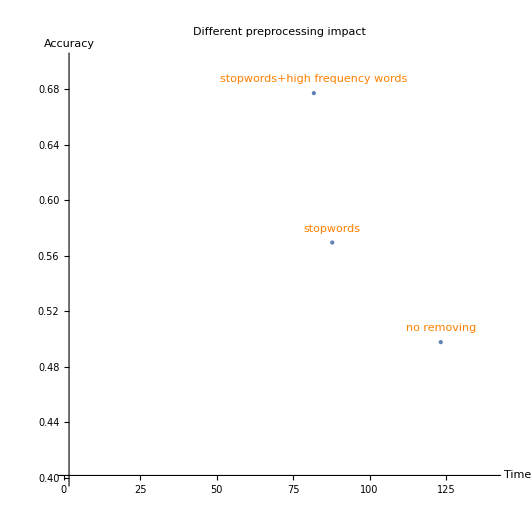

```mathematica
data={rfInfoPre1,rfInfoPre2,rfInfoPre3};
dataPlot=ListPlot[data[[All,{2,3}]],PlotStyle->PointSize->Large,PlotLabel->"Different preprocessing impact",AxesLabel->{"Time","Accuracy"},PlotRange->{{1,140},{0.4,0.7}}];
labels=Text[#[[1]], #[[{2,3}]]+0.01]&/@data;
Show[dataPlot,Graphics[{Orange,labels}],AspectRatio->1,ImageSize->Large]
```

```mathematica
"Based on the above figure,it illustrates that the high-frequency meaningless words we removed doesn't affect training result and on the contrary, it can increase efficiency. Thus, the following codes merely use this training set."
```

#### Run RandomForest for multiple times with different parameters

```mathematica
(*Run Random Forest algorithm many times with different tree numbers*)
clRes=Table[(rf=Classify[train[[1;;2500]],Method->{"RandomForest","TreeNumber"->n}];
cm=ClassifierMeasurements[rf,test[[2;;Length[test]]]];{n,cm["Accuracy"],cm["Precision"],cm["Recall"]}),{n,25,200,25}];
```

```mathematica
ListLinePlot[clRes[[All,{1,2}]],PlotLabel->"Impact of No. of Trees",PlotStyle->PointSize->Large,AxesLabel->{"No. of Tree","Accuracy"},ImageSize->Large]
```

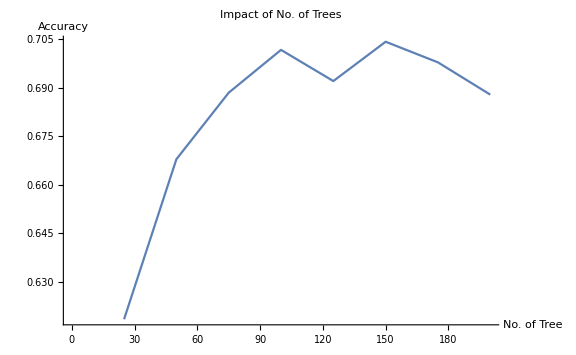

```mathematica
"The above figure demonstrates change of accuracy with increasing number of trees. In generall, limited number of trees is not eligible for learning because the model didn't trained sufficient for the large dimension of features. However, on the other hand, too many tree number performs bad as well. This may due to overfitting. Some meaningless words are put in root or near root in some trees such that they mislead training largely. Based on experiment, the best tree number is between \"100-150\"."
```

#### See the change of accuracy under different training size

```mathematica
rfRes=Table[(rfFunc2=Classify[train[[1;;n]],Method->"RandomForest"];
cm2=ClassifierMeasurements[rfFunc2,test[[2;;Length[test]]]];{n,cm2["Accuracy"],cm2["Precision"],cm2["Recall"]}),{n,500,3000,500}]
```

{{500,0.60375,<|negative→0.562081,positive→0.848907|>,<|negative→0.956308,positive→0.247827|>},{1000,0.691588,<|negative→0.667487,positive→0.724738|>,<|negative→0.769346,positive→0.613087|>},{1500,0.692313,<|negative→0.668593,positive→0.724718|>,<|negative→0.768425,positive→0.615473|>},{2000,0.659875,<|negative→0.760915,positive→0.614284|>,<|negative→0.470938,positive→0.850615|>},{2500,0.675013,<|negative→0.669323,positive→0.681271|>,<|negative→0.697885,positive→0.651922|>},{3000,0.664138,<|negative→0.635804,positive→0.709029|>,<|negative→0.77589,positive→0.551319|>}}

```mathematica
posPrecision=Table[{i*1000,rfRes[[i,3]][[1]]},{i,5}];
negPrecision=Table[{i*1000,rfRes[[i,3]][[2]]},{i,5}];
posRecall=Table[{i*1000,rfRes[[i,4]][[1]]},{i,5}];
negRecall=Table[{i*1000,rfRes[[i,4]][[2]]},{i,5}];
```

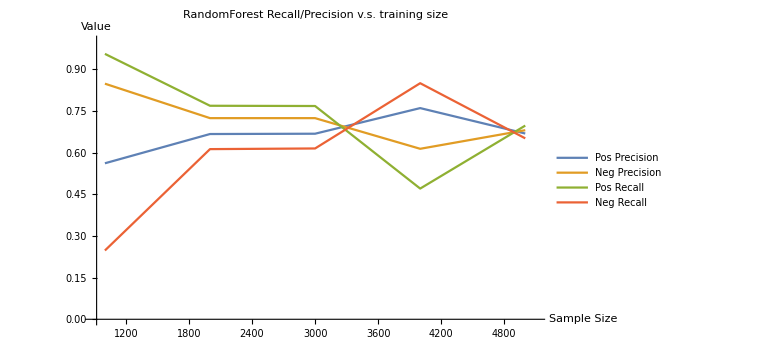

```mathematica
ListLinePlot[{posPrecision,negPrecision,posRecall,negRecall},PlotStyle->PointSize->Large,PlotLabel->"RandomForest Recall/Precision v.s. training size",AxesLabel->{"Sample Size","Value"},PlotRange->{{900,5100},{0,1}},ImageSize->Large,PlotLegends->{"Pos Precision","Neg Precision","Pos Recall","Neg Recall"}]
```

```mathematica
"Since the overall trend of positive recall is decreasing, we conclude that the number of positive reviews the model found decreased. However, the trend of positive precision is opposed, it is becase less negative reviews were judged as positive. In terms of the negative reviews, more and more negative reviews were found as the training size increased.
In general, the major reason is because the number of reviews which are judged as negative grows as the training set size increase."
```

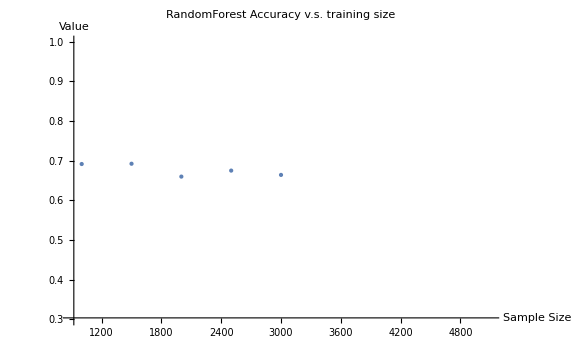

```mathematica
ListPlot[rfRes[[All,{1,2}]],PlotStyle->PointSize->Large,PlotLabel->"RandomForest Accuracy v.s. training size",AxesLabel->{"Sample Size","Value"},PlotRange->{{900,5100},{0.3,1}},ImageSize->Large]
```

```mathematica
"Based on those experiment, I choose data size 5000 for training."
```

#### Result of best random forest model (based on my experiment):

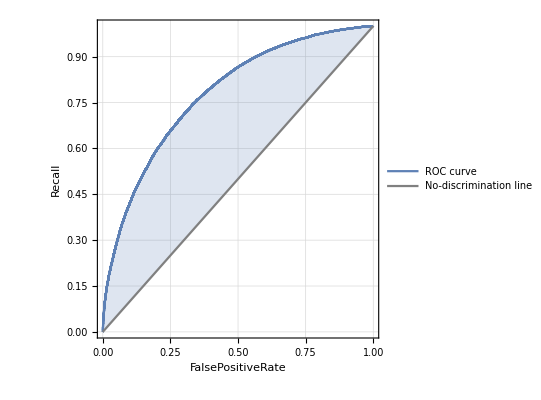
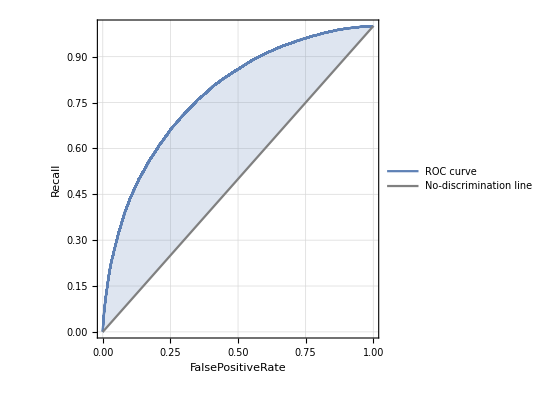
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
cm2["ROCCurve"]
```

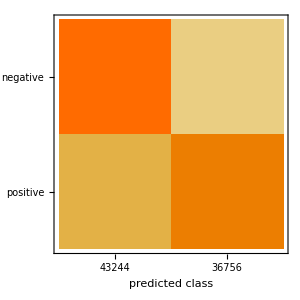

Missing[PropertyNotAvailable,Visualization]

```mathematica
cm2["ConfusionMatrixPlot"]
```

### Neural Networking

#### See the change of Neural Networking with different training set size

```mathematica
nnRes=Table[(nnFunc=Classify[train[[1;;n]],Method->"NeuralNetwork"];
cm2=ClassifierMeasurements[nnFunc,test[[2;;Length[test]]]];{n,cm2["Accuracy"],cm2["Precision"],cm2["Recall"]}),{n,500,3000,500}]
```

{{500,0.772313,<|negative→0.754146,positive→0.793674|>,<|negative→0.811247,positive→0.733007|>},{1000,0.785263,<|negative→0.760913,positive→0.815169|>,<|negative→0.834884,positive→0.735167|>},{1500,0.804675,<|negative→0.795311,positive→0.814814|>,<|negative→0.823016,positive→0.786159|>},{2000,0.803,<|negative→0.848482,positive→0.767531|>,<|negative→0.74001,positive→0.866591|>},{2500,0.810038,<|negative→0.839164,positive→0.78517|>,<|negative→0.769321,positive→0.851143|>},{3000,0.815963,<|negative→0.801135,positive→0.832587|>,<|negative→0.842896,positive→0.788772|>}}

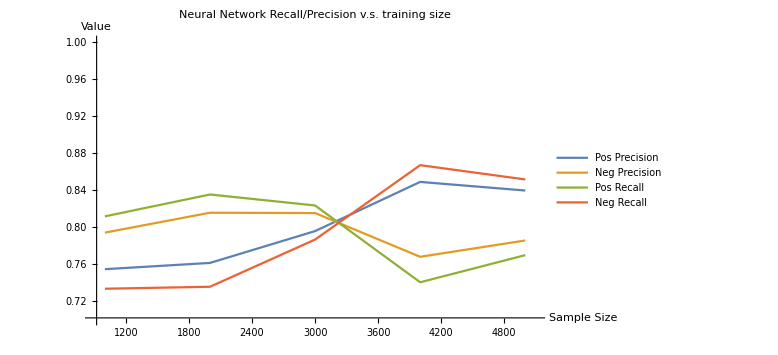

```mathematica
posPrecision=Table[{i*1000,nnRes[[i,3]][[1]]},{i,5}];
negPrecision=Table[{i*1000,nnRes[[i,3]][[2]]},{i,5}];
posRecall=Table[{i*1000,nnRes[[i,4]][[1]]},{i,5}];
negRecall=Table[{i*1000,nnRes[[i,4]][[2]]},{i,5}];
ListLinePlot[{posPrecision,negPrecision,posRecall,negRecall},PlotStyle->PointSize->Large,PlotLabel->"Neural Network Recall/Precision v.s. training size",AxesLabel->{"Sample Size","Value"},PlotRange->{{900,5100},{0.7,1}},ImageSize->Large,PlotLegends->{"Pos Precision","Neg Precision","Pos Recall","Neg Recall"}]
```

```mathematica
"Since the overall trend of positive recall is decreasing, we conclude that the number of positive reviews the model found decreased. However, the trend of positive precision is opposed, it is becase less negative reviews were judged as positive. In terms of the negative reviews, more and more negative reviews were found as the training size increased.
In general, the major reason is because the number of reviews which are judged as negative grows as the training set size increase."
```

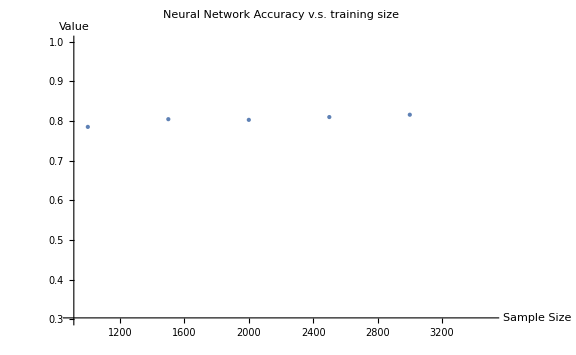

```mathematica
ListPlot[nnRes[[All,{1,2}]],PlotStyle->PointSize->Large,PlotLabel->"Neural Network Accuracy v.s. training size",AxesLabel->{"Sample Size","Value"},PlotRange->{{900,3500},{0.3,1}},ImageSize->Large]
```

```mathematica
"From the above plot, we knew that the Neural Network performs quiet well when the training set size increases. So I use 3000 as the training set size for the following measurements."
```

```mathematica
Result of the best Neural Network model (Based on my experiment)
```

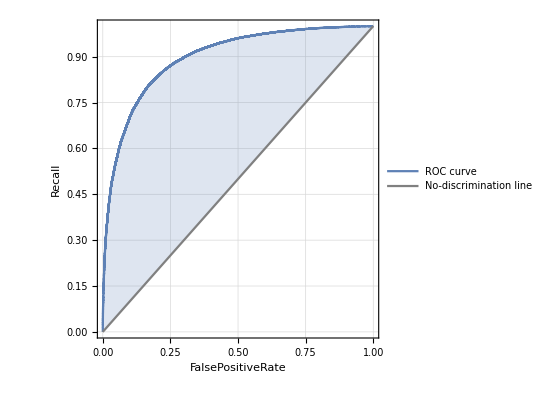
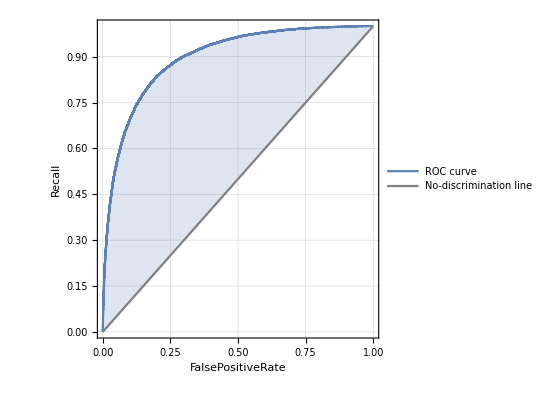
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
cm2["ROCCurve"]
```

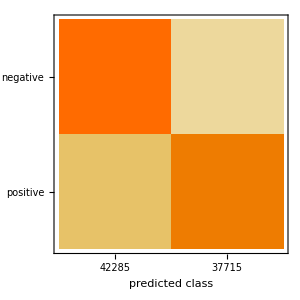

```mathematica
cm2["ConfusionMatrixPlot"]
```

### Support Vector Machine

#### Let’s compare the performance of different preprocessed training set.

```mathematica
svmPre1=Classify[train[[1;;2000]],Method->"SupportVectorMachine"]
svmPre2=Classify[train2[[1;;2000]],Method->"SupportVectorMachine"]
svmPre3=Classify[train3[[1;;2000]],Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

ClassifierFunction[…]

ClassifierFunction[…]

```mathematica
svmInfoPre1={"stopwords+high frequency words",QuantityMagnitude[ClassifierInformation[rfPre1,"TrainingTime"]],ClassifierMeasurements[svmPre1,test[[2;;]],"Accuracy"]};
svmInfoPre2={"stopwords",QuantityMagnitude[ClassifierInformation[rfPre2,"TrainingTime"]],ClassifierMeasurements[svmPre2,test[[2;;]],"Accuracy"]};
svmInfoPre3={"no removing",QuantityMagnitude[ClassifierInformation[rfPre3,"TrainingTime"]],ClassifierMeasurements[svmPre3,test[[2;;]],"Accuracy"]}
```

{no removing,100.626,0.497625}

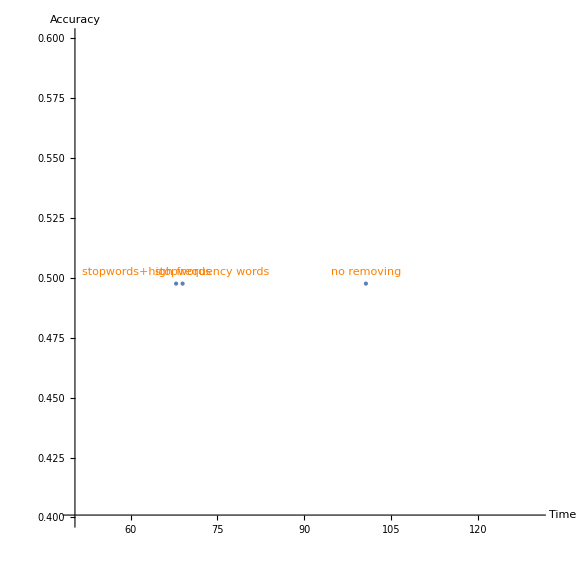

```mathematica
dataSvm={svmInfoPre1,svmInfoPre2,svmInfoPre3};
dataSvmPlot=ListPlot[dataSvm[[All,{2,3}]],PlotStyle->PointSize->Large,AxesLabel->{"Time","Accuracy"},PlotRange->{{50,130},{0.4,0.6}}];
labels=Text[#[[1]], #[[{2,3}]]+0.005]&/@dataSvm;
Show[dataSvmPlot,Graphics[{Orange,labels}],AspectRatio->1,ImageSize->Large]
```

```mathematica
"The above picture shows the impact of different kinds of preprocessing on training time and accuracy. Since the accuracy doesn't have much different, we prefer to use a more efficient way,namely removing both stopwords and high frequency words."
```

#### Run SVM multiple times with different parameters

```mathematica
svm1=Classify[train[[1;;2500]],Method->{"SupportVectorMachine","KernelType"->"Linear"}];
svm2=Classify[train[[1;;2500]],Method->{"SupportVectorMachine","KernelType"->"RadialBasisFunction","MulticlassMethod"->"OneVersusOne"}];
svm3=Classify[train[[1;;2500]],Method->{"SupportVectorMachine","KernelType"->"Sigmoid"}];
svm4=Classify[train[[1;;2500]],Method->{"SupportVectorMachine","KernelType"->"Polynomial"}];
```

ClassifierFunction[…]

ClassifierFunction[…]

ClassifierFunction[…]

«1 more identical outputs»

```mathematica
svmc1={"Linear",1,ClassifierMeasurements[svm1,test[[2;;Length[test]]],"Accuracy"]};
svmc2={"Radial Basis",2,ClassifierMeasurements[svm2,test[[2;;Length[test]]],"Accuracy"]};
svmc3={"Sigmoid",3,ClassifierMeasurements[svm3,test[[2;;Length[test]]],"Accuracy"]};
svmc4={"Polynomial",4,ClassifierMeasurements[svm4,test[[2;;Length[test]]],"Accuracy"]};
```

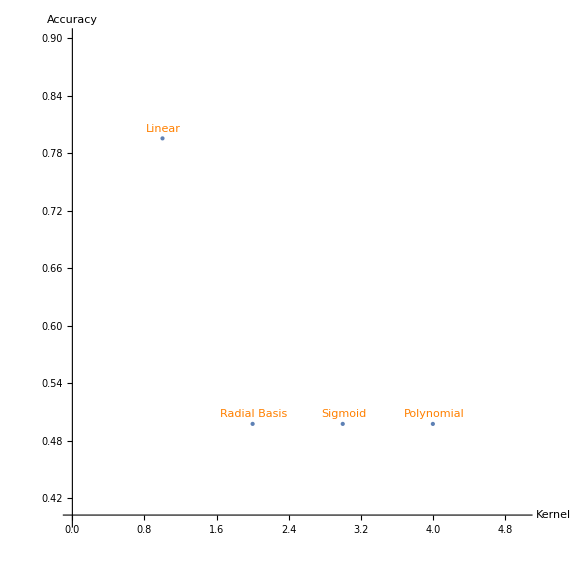

```mathematica
data={svmc1,svmc2,svmc3,svmc4};
dataPlot=ListPlot[data[[All,{2,3}]],PlotStyle->PointSize->Large,AxesLabel->{"Kernel","Accuracy"},PlotRange->{{0,5},{0.4,0.9}}];
labels=Text[#[[1]], #[[{2,3}]]+0.01]&/@data;
Show[dataPlot,Graphics[{Orange,labels}],AspectRatio->1,ImageSize->Large]
```

```mathematica
"Because SVM creates another dimension such that we are more likely to make the test data linear-seperable."
```

#### See the change of SVM accuracy under different training size

```mathematica
svmRes=Table[(svmFunc2=Classify[train[[1;;n]],Method->{"SupportVectorMachine","KernelType"->"Linear","SoftMarginParameter"->2}];
cm2=ClassifierMeasurements[svmFunc2,test[[2;;Length[test]]]];{n,cm2["Accuracy"],cm2["Precision"],cm2["Recall"]}),{n,500,3000,500}]
```

{{500,0.75845,<|negative→0.78088,positive→0.73901|>,<|negative→0.721697,positive→0.795554|>},{1000,0.768013,<|negative→0.809784,positive→0.735667|>,<|negative→0.703459,positive→0.833183|>},{1500,0.778013,<|negative→0.789784,positive→0.766981|>,<|negative→0.760562,positive→0.795629|>},{2000,0.780938,<|negative→0.776868,positive→0.785201|>,<|negative→0.791192,positive→0.770585|>},{2500,0.785375,<|negative→0.794253,positive→0.776881|>,<|negative→0.773028,positive→0.79784|>},{3000,0.789663,<|negative→0.78172,positive→0.798209|>,<|negative→0.806519,positive→0.772645|>}}

```mathematica
posPrecision=Table[{i*1000,svmRes[[i,3]][[1]]},{i,5}];
negPrecision=Table[{i*1000,svmRes[[i,3]][[2]]},{i,5}];
posRecall=Table[{i*1000,svmRes[[i,4]][[1]]},{i,5}];
negRecall=Table[{i*1000,svmRes[[i,4]][[2]]},{i,5}];
```

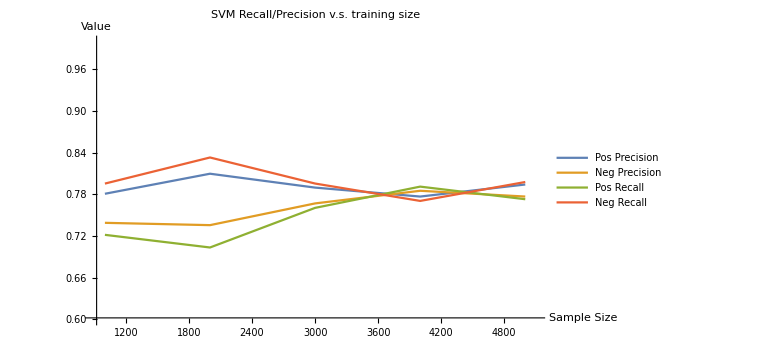

```mathematica
ListLinePlot[{posPrecision,negPrecision,posRecall,negRecall},PlotStyle->PointSize->Large,PlotLabel->"SVM Recall/Precision v.s. training size",AxesLabel->{"Sample Size","Value"},PlotRange->{{900,5100},{0.6,1}},ImageSize->Large,PlotLegends->{"Pos Precision","Neg Precision","Pos Recall","Neg Recall"}]
```

```mathematica
"Different from the previous two algorithms, since the overall trend of positive recall increased, we conclude that the number of positive reviews the model found grown. On the contrary, the negative recall decreased as size got large.
In general, the major reason is because the number of reviews which are labeled positive grows as the training set size increase."
```

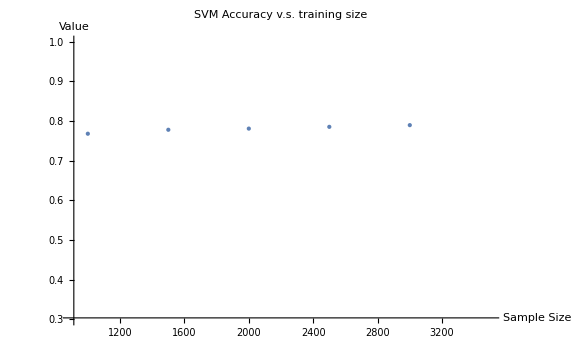

```mathematica
ListPlot[svmRes[[All,{1,2}]],PlotStyle->PointSize->Large,PlotLabel->"SVM Accuracy v.s. training size",AxesLabel->{"Sample Size","Value"},PlotRange->{{900,3500},{0.3,1}},ImageSize->Large]
```

```mathematica
As shown in above figure, the model has the best performance when training set size is 2500. So the following test will focus on the size 2500.
Result of best SVM model (Based on my experiment)
```

```mathematica
svm=Classify[train[[1;;2500]],Method->{"SupportVectorMachine","KernelType"->"Linear","SoftMarginParameter"->2}];
cm=ClassifierMeasurements[svm,test[[2;;]]]
```

ClassifierMeasurementsObject[…]

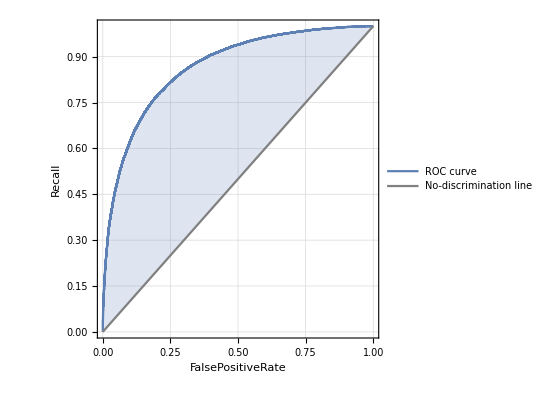
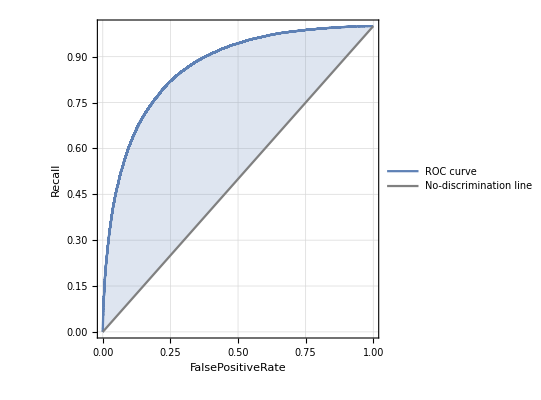
<|negative→-Graphics-,positive→-Graphics-|>

```mathematica
cm["ROCCurve"]
```

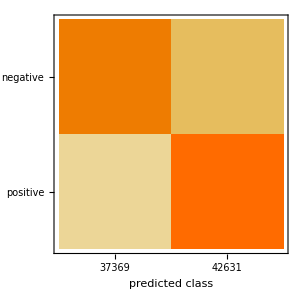

```mathematica
cm["ConfusionMatrixPlot"]
```

## Analysis

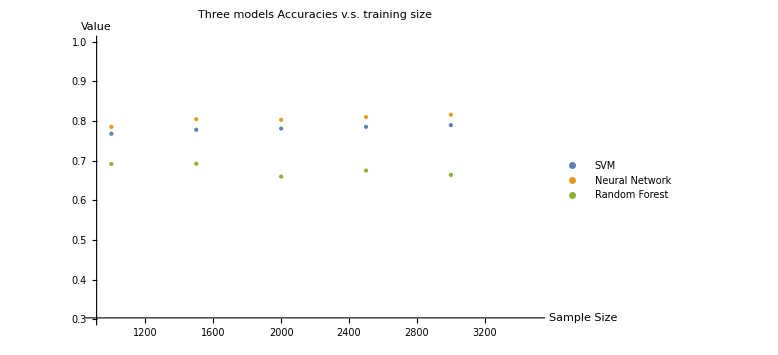

```mathematica
ListPlot[{svmRes[[All,{1,2}]],nnRes[[All,{1,2}]],rfRes[[All,{1,2}]]},PlotStyle->PointSize->Large,PlotLabel->"Three models Accuracies v.s. training size",AxesLabel->{"Sample Size","Value"},PlotRange->{{900,3500},{0.3,1}},ImageSize->Large,PlotLegends->{"SVM","Neural Network","Random Forest"}]
```

```mathematica
"This figure illustrates the different performances of three chosen algorithm: RandomForest, SVM and Neural Network. 

General Analysis:
From the ROC Curves drawn in the previous section, we inferred that all of those three algorithm performed not bad on this dataset because all of those curves were in the left corner. When the the size of training dataset rised up, the accuracy didn't guarantee to grow because larger dataset also brings in larger noises. According to 3 precision/recall plots in the above section, we prove that the accuracy is orthogonal to precision. That is, the higher accuracy value is the larger precision is.

Compared Analysis:
Except for RandomForest, both of other two algorithms have accuracy higher than 70%. Even though compared with other two algorithms, RandomForest is much easier to train, the lower accuracy frustrates me to select it. In my opinion, 
1. the major reason triggers this is overfitting. Even though a Decision Tree perfer to reduce as much entropy value as possible, random forest has several trees so that there may be one tree emphasize the impacts of useless words. 
2. Another reason perhaps due to the not balanced training data. From our observation, the number of positive data is more than the number of negative from the first 2500 sentences, which can bias random forest in favor of those attributes with more items.

There are 2 main reason for me to choose SVM as the additional algorithm:
1. SVM can create anther dimension for input data such that the input data can become linear separable. In other word, the training time should be fancy.
2. The support vectors are responsible for enlarging margin between items and hyperplane, therefore, this algorithm is more likely to find best way to category reviews with different sentiments.

Approximately 80% accuracy shows success of Neural Network and SVM. Even though Neural Network is more eligible for continuous data, increasing the hidden layer could improve the accuracy dramatically. The reason why I choose SVM is quiet obvious. Based on our experiment, first and foremost, the performance of SVM is wonderful. Besides this, SVM is also efficent to process high dimension data because it can create another dimension and put data into it. With less training time and good accuracy, I conclude that the SVM is more feasible for this dataset than the other two."
```